BEAM DYNAMICS IN UNDULATOR

```mathematica
q=1; m=1; c=1;
B0=1;λp=2π; γ=10; β=√(1-1/γ^2);

K=(q B0 λp)/(2 π m c^2) (*undulator parameter*)

βavg = β(1-K^2/(4 γ^2)) (*averaged velocity*)
```

1

(1197 √11)/4000

```mathematica
Σ1=Function[{k,μ,ν},Sum[BesselJ[-m,μ]*BesselJ[k-2*m,ν],{m,-10,10}]]
Σ2=Function[{k,μ,ν},Sum[BesselJ[-m,μ]*(BesselJ[k-2*m-1,ν]+BesselJ[k-2*m+1,ν]),{m,-10,10}]]
```

Function[{k,μ,ν},∑_(m=-10)^10 BesselJ[-m,μ] BesselJ[k-2 m,ν]]

Function[{k,μ,ν},∑_(m=-10)^10 BesselJ[-m,μ] (BesselJ[k-2 m-1,ν]+BesselJ[k-2 m+1,ν])]

```mathematica
Iσk = Function[{θ,ϕ},(2 γ θ )^2/((1+K^2/2+γ^2θ^2)^2)]
```

```mathematica
dNphdΩ = α γ^2 βavg^2 Np^2 *Δω/ω Sum[k^2(Sin[π Np Δω/ω]/(π Np Δω/ω))^2(Iσk + Iπk),{k,1,10}]
```

```mathematica
r=1;
gm=5;
wc=1.5 gm^3 ;
wwc=w/wc;
gmth=gm*th;
chi=0.5 wwc (1+gmth^2)^1.5;
```

```mathematica
dIdwdOSIG=Function[{th,w},wwc^2 (1+gmth^2)^2 (BesselK[2/3,chi]^2)];
dIdwdOPI=Function[{th,w},wwc^2 (1+gmth^2)^2 (gmth^2/(1+gmth^2))(BesselK[2/3,chi]^2)];
dIdw=Function[{wwc},gm wwc NIntegrate[BesselK[5/3,x],{x,wwc,100*wwc}]];
```

```mathematica
plt1=ContourPlot[dIdwdOSIG[gmth,wwc],{th,-3,3},{w,0,10},Contours->20,PlotRange->{0,2},PlotLabel->Style["σ mode",24],Frame->True,FrameLabel->{"γθ","ω/ω_c"}];
```

```mathematica
plt2=ContourPlot[dIdwdOPI[gmth,wwc],{th,-3,3},{w,0,10},Contours->20,PlotRange->{0,0.5},PlotLabel->Style["π mode",24],Frame->True,FrameLabel->{"γθ","ω/ω_c"}];
```

```mathematica
plt3=Plot[dIdw[wwc],{wwc,0,3},PlotLabel->Style["Radiation Spectrum",24],Frame->True,FrameLabel->{"ω/ω_c","dI/dω"}];
```

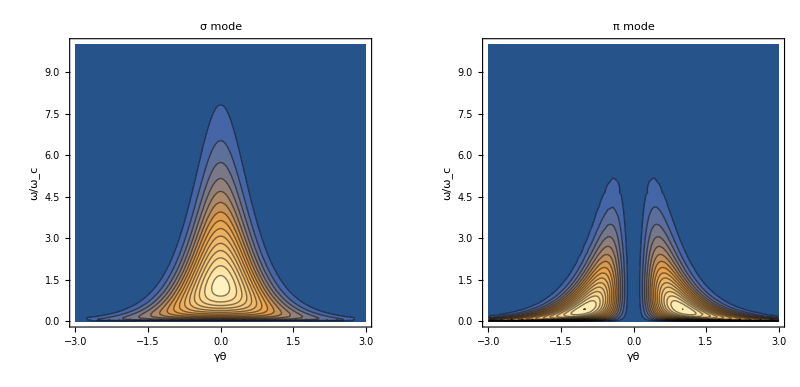

```mathematica
GraphicsRow[{plt1,plt2},ImageSize->Full]
```

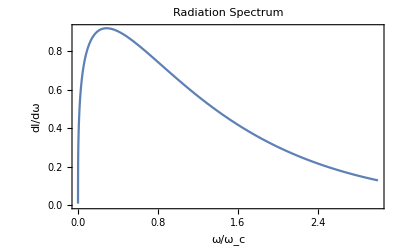

```mathematica
GraphicsRow[{plt3},ImageSize->600]
```

GAUSSIAN MODE

```mathematica
E0=1;
w0=1;
zR=1;
k=1;

r=Function[{x,y,z},Sqrt[x^2+y^2+z^2]]
w=Function[z,w0 Sqrt[1+(z/zR)^2]]
R=Function[z,z (1+(z/zR)^2)]
ϕ=Function[z,ArcTan[z/zR]]
Ee=Function[{x,y,z},E0 w0/w[z] Exp[-r[x,y,z]^2/w[z]] Exp[-I (k z + k  r[x,y,z]^2/(2 R[z]) - ϕ[z])]]
```

Function[{x,y,z},√(x^2+y^2+z^2)]

Function[z,w0 √(1+(z/zR)^2)]

Function[z,z (1+(z/zR)^2)]

Function[z,ArcTan[z/zR]]

Function[{x,y,z},(E0 w0 Exp[-r[x,y,z]^2/w[z]] Exp[-ⅈ (k z+(k r[x,y,z]^2)/(2 R[z])-ϕ[z])])/w[z]]

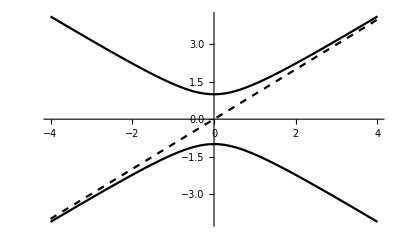

```mathematica
Plot[{w[z],-w[z],z},{z,-4,4},PlotStyle->{Black,Black,Directive[Black,Dashed]}]
```